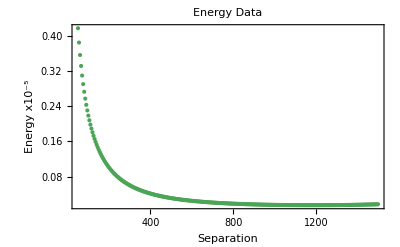

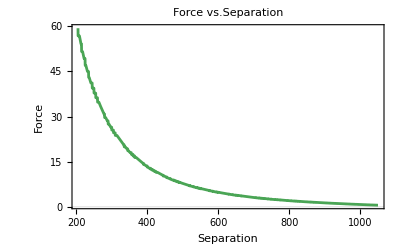

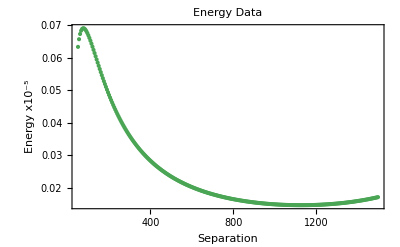

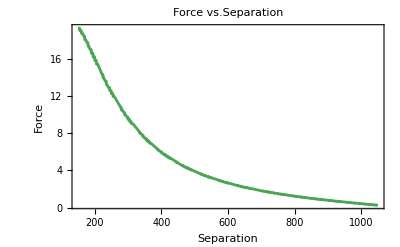

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]

files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString];
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/negative"];
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString];
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)

SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
(*Print[SolveForce["energysep.txt"]];*)
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}];
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]];
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}];
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];

SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
(*Print[SolveForce["energysep2.txt"]];*)
allData2=SolveForce["energysep2.txt"];
{sep2, energy2}= Transpose[allData2];
showData2 = Transpose[{sep2,Map[#/(10^5)&,energy2//N]}];
energyGraph2 = ListPlot[showData2, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]];
(*ListPlot[allData,Joined->True]*)
force2[x_]=-D[Interpolation[allData2,InterpolationOrder->1][x],x];
forceGraph2 = Plot[force2[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}];
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];

energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full,  PlotRange->All]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full, PlotRange->All]

energyGraphnice2 = Show[energyGraph2,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full,  PlotRange->All]
forceGraphnice2 = Show[forceGraph2,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full, PlotRange->All]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/negative"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2,minz,maxz},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
minz=Min[Transpose[data][[3]]];
maxz=Max[Transpose[data][[3]]];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{minz,maxz}];
prettyData
]
prettySurface["surface0negative.gpl"]
Show[prettySurface["surface0negative.gpl"],Axes->True,AxesStyle->Black]
```

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[
Show[prettySurface[
StringJoin["surface",ToString[IntegerPart[i]],"positive.gpl"]
],Axes->True,AxesStyle->Black,PlotRange->{Automatic,Automatic,{-600,0}},ViewPoint->{0,-∞,0}]
,{i,0,290,1}]
```

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot3D[ReadList[$Failed,{Number,Number,Number}],Mesh→10,InterpolationOrder→3,ColorFunction→Function[{x,y,z},colorScheme[z]],BoxRatios→Automatic,PlotStyle→Opacity[0.9],Boxed→False,Axes→False,Background→None,PlotRange→{{-300,300},{-150,150},Automatic}],].

Show::gtype: Show is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::partw: Part 3 of Transpose[ReadList[$Failed,{Number,Number,Number}]] does not exist.

System`ListPlotsDump`fn::prng: Value of option PlotRange -> {Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧,Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::partw: Part 3 of Transpose[ReadList[$Failed,{Number,Number,Number}]] does not exist.

System`ListPlotsDump`fn::prng: Value of option PlotRange -> {Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧,Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::partw: Part 3 of Transpose[ReadList[$Failed,{Number,Number,Number}]] does not exist.

System`ListPlotsDump`fn::prng: Value of option PlotRange -> {Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧,Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::partw: Part 3 of Transpose[ReadList[$Failed,{Number,Number,Number}]] does not exist.

System`ListPlotsDump`fn::prng: Value of option PlotRange -> {Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧,Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

OpenRead::noopen: Cannot open surface0positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::partw: Part 3 of Transpose[ReadList[$Failed,{Number,Number,Number}]] does not exist.

System`ListPlotsDump`fn::prng: Value of option PlotRange -> {Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧,Transpose[ReadList[$Failed,{Number,Number,Number}]]⟦3⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface150positive.gpl"]
```

OpenRead::noopen: Cannot open surface150positive.gpl.

Skip::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ListPlot3D::arrayerr: ReadList[$Failed,{Number,Number,Number}] must be a valid array or a list of valid arrays.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot3D[ReadList[$Failed,{Number,Number,Number}],Mesh→10,InterpolationOrder→3,ColorFunction→Function[{x,y,z},colorScheme[z]],BoxRatios→Automatic,PlotStyle→Opacity[0.9],Boxed→False,Axes→False,Background→None,PlotRange→{{-300,300},{-150,150},Automatic}],].

Show[ListPlot3D[ReadList[$Failed,{Number,Number,Number}],Mesh→10,InterpolationOrder→3,ColorFunction→Function[{x,y,z},colorScheme[z]],BoxRatios→Automatic,PlotStyle→Opacity[0.9],Boxed→False,Axes→False,Background→None,PlotRange→{{-300,300},{-150,150},Automatic}],-Graphics3D-]

```mathematica
|
```